```mathematica
(*TL*)
```

```mathematica
(*simple reps for characteristic zero*)
ecoeff[n_,k_,l_]:=
Which[k>n,0,k==n,1,Mod[k,l]==0,0,Mod[k,l]==2&&(Mod[n-k,2*l]==0),1,Mod[k,l]==2&& (Mod[n-k,2*l]==2),-1,Mod[k,l]==2,0,Mod[k,l]==1&&(Mod[n-k-4,2*l]==0),-1,Mod[k,l]==1&&(Mod[n-k-4,2*l]==2),1,Mod[k,l]==1,0]
simpletl [n_,k_]:=Sum[ecoeff[n-2*r+1,k+1,3]*((n-2*r+1)/(n-r+1))*Binomial[n,r],{r,0,(n-k)/2}]
```

```mathematica
(*size of monoid*)
Asymptotic[1/(2n+1)*Binomial[4n,2n],n->Infinity]
```

2^(-3/2+4 n)/(n^(3/2) √π)

```mathematica
(*RTL*)
```

```mathematica
(*simple rep plot for n=100*)
Plot[Binomial[100-1,1/2*(2*100-k)],{k,50,150},GridLines->{{{100+1-Sqrt[2*100],Thick},{100+1+Sqrt[2*100],Thick},{100+1,Dashed}}},PlotRange->All]
```

-Graphics-

```mathematica
(*rep gap upper bound*)
Asymptotic[Binomial[n-1,1/2*(n-1)],n->Infinity]
```

2^(-1/2+n)/(√n √π)

```mathematica
(*rep gap lower bound*)
Asymptotic[FunctionExpand[Binomial[n-1,1/2*(2n-((n+1))-Sqrt[2n])]],n->Infinity]
```

(2^(-1/2+n) ⅇ^(-1-1/(3 n)))/(√n √π)

```mathematica
(*size of monoid*)
Asymptotic[Binomial[2n-1,n],n->Infinity]
```

2^(-1+2 n)/(√n √π)

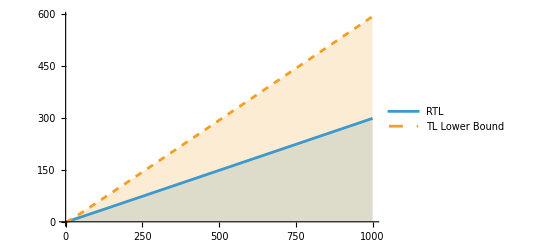

```mathematica
(*comparison of rep gaps*)
DiscretePlot[{Log10[Binomial[n-1,1/2*(n-1)]],Log10[2^(2n)*(2n)^(-5/2)]},{n,0,1000},PlotLegends->Placed[{"RTL","TL Lower Bound"},Above],PlotStyle->{Automatic,Dashed}]
```

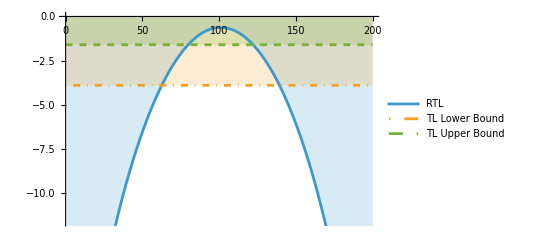

```mathematica
(*comparison of gap ratios for n=100*)
DiscretePlot[{Log10[Binomial[100-1,1/2*(2*100-k)]/Sqrt[Binomial[2*100-1,100]]],Log10[2^(2*100)*(2*100)^(-5/2)/Sqrt[1/(2*100+1)*Binomial[4*100,2*100]]],Log10[2^(2*100)*(2*100)^(-3/2)/Sqrt[1/(2*100+1)*Binomial[4*100,2*100]]]},{k,0,2*100},PlotLegends->Placed[{"RTL","TL Lower Bound","TL Upper Bound"},Above],GridLines->{{{100+1-Sqrt[2*100],Thick},{100+1+Sqrt[2*100],Thick}}},PlotStyle->{Automatic,DotDashed,Dashed}]
```

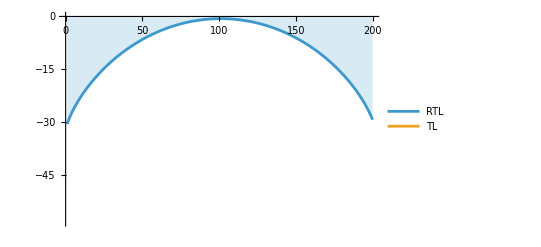

```mathematica
(*Direct comparison of the ratios for n=100*)
DiscretePlot[{Log10[Binomial[100-1,1/2*(2*100-k)]/Sqrt[Binomial[2*100-1,100]]],Log10[simpletl[2*100,k]/Sqrt[1/(2*100+1)*Binomial[4*100,2*100]]]},{k,0,2*100},PlotLegends->{"RTL","TL"}]
```